```mathematica
Once[<<MaTeX`]
```

5+4 z-4 z^3+z^4

{-0.661676-0.602469 ⅈ,-0.661676+0.602469 ⅈ,1.74481,3.57854}

(-5+z^3 (-8+3 z))/(4+4 (-3+z) z^2)

CompiledFunction[…]

4.29425

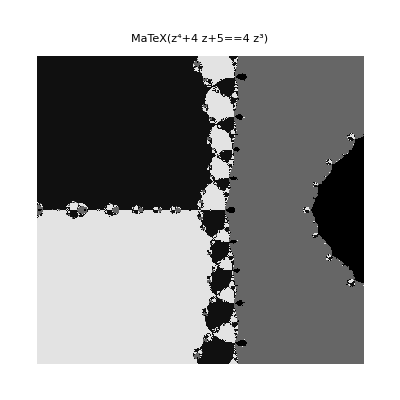

```mathematica
fun=Evaluate[RandomInteger[{-5,5},5].{1,z,z^2,z^3,z^4}];If[D[fun, z]===0,fun=z^4-1,fun]
sol=z/.NSolve[%==0,z]
ne[z_]=HornerForm[z-#/D[#, z]&@fun]//FullSimplify
newt=Compile[{{zn,_Complex},{n,_Integer}},Module[{z=zn},Catch[Do[If[Abs[z]>10000,Throw[0],z=ne[z]],n];1+Arg[z]+Abs[z]]]]
Module[{zf=1.2Max[Abs[sol]],pp=400},Print[zf];ArrayPlot[ParallelTable[newt[x+ⅈ y,800],{y,-zf,zf,2(zf/(pp+0.101))},{x,-zf,zf,2(zf/(pp+0.101))}],DataReversed->True,DataRange->{{-zf,zf},{-zf,zf}},PlotLabel->MaTeX[FullSimplify[fun==0]],ImageSize->pp,ColorFunctionScaling->True]]
```